```mathematica
SetDirectory["D:\\M.Sc\\Forth_Sem_Project\\Projects\\output\\"]
```

D:\M.Sc\Forth_Sem_Project\Projects\output

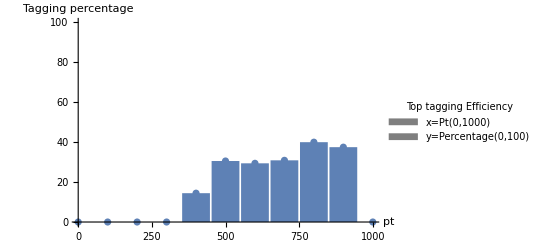

```mathematica
sd=ImportString[StringReplace[Import["D:\\M.Sc\\Forth_Sem_Project\\Projects\\output\\06-boosted_top_multev_histg.out","Text"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"Table"];
hist1[dat_]:=dat[[1]];
hist2[dat_]:={dat[[1]],dat[[4]]}; 
histp= hist2/@sd;
histc = hist1/@sd;
legend=SwatchLegend[{Red,Blue},{"x=Pt(0,1000)","y=Percentage(0,100)"},LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->"Top tagging Efficiency",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5];
h=ListPlot[histp,AxesLabel->{"pt", "Tagging percentage"},(* Ticks->{ Automatic,Automatic} ,*)(*Frame->True,FrameStyle->{Thick,Directive[Orange,12,Thick]},*)PlotRange->{Automatic,{0,100} },(*Epilog->Inset[Framed[Style["Spiral",20],Background->LightYellow],{1,1},{1,1}],*)PlotLegends->Placed[legend,{{.8,0.9},{0.7,0.8}}],
AxesStyle->Directive[Orange,12,Thick] ,Filling->Bottom, FillingStyle->Thickness[0.05],LabelStyle->Directive[Bold, Medium]]
Export["D:\\M.Sc\\Forth_Sem_Project\\Projects\\plots\\top_eff_hist.png",h,"PNG"];
```

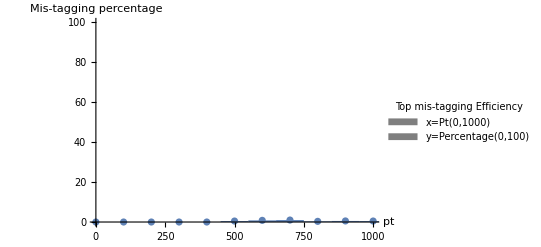

```mathematica
sd=ImportString[StringReplace[Import["D:\\M.Sc\\Forth_Sem_Project\\Projects\\output\\06-boosted_top_multev_dijet.out","Text"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"Table"];
hist1[dat_]:=dat[[1]];
hist2[dat_]:={dat[[1]],dat[[4]]}; 
histp= hist2/@sd;
histc = hist1/@sd;
legend=SwatchLegend[{Red,Blue},{"x=Pt(0,1000)","y=Percentage(0,100)"},LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->"Top mis-tagging Efficiency",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5];
h1=ListPlot[histp,AxesLabel->{"pt", "Mis-tagging percentage"},(* Ticks->{ Automatic,Automatic} ,*)(*Frame->True,FrameStyle->{Thick,Directive[Orange,12,Thick]},*)PlotRange->{Automatic,{0,100} },PlotLegends->Placed[legend,{{.8,0.9},{0.7,0.8}}],
AxesStyle->Directive[Orange,12,Thick] ,Filling->Bottom, FillingStyle->Thickness[0.05],LabelStyle->Directive[Bold, Medium]]
Export["D:\\M.Sc\\Forth_Sem_Project\\Projects\\plots\\top_mist_eff_hist.png",h1,"PNG"];
```

```mathematica
(*************************tagged constituents********************************)
sd=ImportString[StringReplace[Import["D:\\M.Sc\\Forth_Sem_Project\\Projects\\output\\06-boosted_top_multev_tagged.out","Text"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"Table"];
datat[dat_]:={dat[[2]],dat[[3]],dat[[4]]};
(*datat2d[dat_]:={dat[[2]],dat[[3]]};*)
tdata = datat/@sd;
(*tdata2d = datat2d/@sd;*)
datad[dat_]:= dat[[4]];
ddata = datad/@sd;
Max[ddata];
m=Max[Max[ddata],Max[ddata]];
g=ListPointPlot3D[tdata,AxesOrigin->{0,0,0},  AxesLabel->{"ita","phi","pt"} ,PlotRange->{{-4,4},{0,6.28},{0,m}}, ImageSize->400,BoxRatios->1 ,
ViewPoint->{0,0,1000}(*{-10,-10,5}*),AxesStyle->Directive[Black, 12,Thin] ,BoxStyle->Directive[ Purple],LabelStyle->Directive[Black,Thin],ColorFunction->Function[{x,y,z},ColorData[{"Rainbow",{0,.3}}][z]],Ticks->{ Automatic,Automatic,Automatic}, PlotLegends->BarLegend[{"Rainbow",{0,m }}]];
s3=Show[g,ViewPoint->{-8,15,5}];
s4=Show[g,ViewPoint->{0,0,1000}];
Export["D:\\M.Sc\\Forth_Sem_Project\\Projects\\plots\\tagged.gif",{s3,s4},DisplayDurations->2]
```

-Graphics3D-

D:\M.Sc\Forth_Sem_Project\Projects\plots\tagged.gif

```mathematica
"D:\\M.Sc\\Forth_Sem_Project\\Projects\\plots\\tagged.gif"
```

```mathematica
(*************************untagged constituents********************************)
sd=ImportString[StringReplace[Import["D:\\M.Sc\\Forth_Sem_Project\\Projects\\output\\06-boosted_top_multev_untagged.out","Text"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"Table"];
datat[dat_]:={dat[[2]],dat[[3]],dat[[4]]};
(*datat2d[dat_]:={dat[[2]],dat[[3]]};*)
tdata = datat/@sd;
(*tdata2d = datat2d/@sd;*)
datad[dat_]:= dat[[4]];
ddata = datad/@sd;
Max[ddata];
m=Max[Max[ddata],Max[ddata]];
g1=ListPointPlot3D[tdata,AxesOrigin->{0,0,0},  AxesLabel->{"ita","phi","pt"} ,PlotRange->{{-4,4},{0,6.28},{0,m}}, ImageSize->400,BoxRatios->1 ,
ViewPoint->{0,0,1000}(*{-10,-10,5}*),AxesStyle->Directive[Black, 12,Thin] ,BoxStyle->Directive[ Purple],LabelStyle->Directive[Black,Thin],ColorFunction->Function[{x,y,z},ColorData[{"Rainbow",{0,.3}}][z]],Ticks->{ Automatic,Automatic,Automatic}, PlotLegends->BarLegend[{"Rainbow",{0,m }}]];
s1=Show[g1,ViewPoint->{10,0,1}];
s2=Show[g1,ViewPoint->{0,0,1000}];
Export["D:\\M.Sc\\Forth_Sem_Project\\Projects\\plots\\untagged.gif",{s1,s2},DisplayDurations->2]
```

D:\M.Sc\Forth_Sem_Project\Projects\plots\untagged.gif

```mathematica
"D:\\M.Sc\\Forth_Sem_Project\\Projects\\plots\\untagged.gif"
```